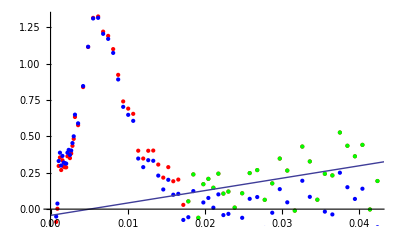

{-0.0430741+8.52084 x, | Estimate | Standard Error | t-Statistic | P-Value
a | 8.52084 | 3.37823 | 2.52228 | 0.0178619
b | -0.0430741 | 0.101843 | -0.422945 | 0.675685}

```mathematica
prefix = "PET-";
sample = "215";
path = ParentDirectory[NotebookDirectory[]] <> "/data/" <> prefix <> sample;
rawData=Import[path<>".0.phg","Table"];

data = Take[rawData, -(Length[rawData]-7)];

toRel[array_] := {array[[1]]/(2*Pi), array[[2]]*(array[[1]] /(2*Pi))^2};
toRelError[array_] := {array[[1]]/(2*Pi), array[[2]]*(array[[1]] /(2*Pi))^2, array[[3]]*(array[[1]] /(2*Pi))^2};
rel = Map[toRel, data];

sample = 28;
notSample = Length[data ] - sample;

linearData =  Take[rel, -sample];
nonLinearData = Take[rel, Length[data ] - sample];
lFit = NonlinearModelFit[linearData,a x + b,{a,b},{x}];

correct[a_] := {a[[1]], a[[2]]-lFit["Function"][a[[1]]]}
correctedRel = Map[correct, rel];


Show[ListPlot[rel,PlotStyle->Red], ListPlot[correctedRel,PlotStyle->Blue], ListPlot[linearData,PlotStyle->Green],Plot[{lFit["BestFit"]},{x,0,0.044}]]

lFit[{"BestFit","ParameterTable"}]

switch[a_] := {a[[2]], a[[1]]}
correctedRelOutput = Map[switch, correctedRel];

Export[path<>".rel", correctedRelOutput, "Table"];
Export[path <> ".fit", lFit["BestFit"], "String"];
Export[path<>"-fitPoints.rel", linearData, "Table"];
Export[path<>"-nonFitPoints.rel", nonLinearData, "Table"];
```